```mathematica
ClearAll["Global`", Subscript]
```

```mathematica
$Assumptions=M>0&& ℏ>0&& ω>0 && Element[{Subscript[x, 1],C[1]},Reals]
```

M>0&&ℏ>0&&ω>0&&(x_1|C[1])∈ℝ

```mathematica
X = {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}
```

{x_1,x_2,x_3}

```mathematica
Ψ = Subscript[ψ, 1][Subscript[x, 1]]  Subscript[ψ, 2][Subscript[x, 2]]  Subscript[ψ, 3][Subscript[x, 3]]
```

ψ_1[x_1] ψ_2[x_2] ψ_3[x_3]

```mathematica
a =Table[With [{Xn = X[[n]]},1/Sqrt[2 M ℏ ω] (-I ℏ D[#,Xn] -I M ω Xn  #) &], {n,1,3}]
```

{(-ⅈ ℏ ∂_x_1 #1-ⅈ M ω x_1 #1)/(√(2 M ℏ ω))&,(-ⅈ ℏ ∂_x_2 #1-ⅈ M ω x_2 #1)/(√(2 M ℏ ω))&,(-ⅈ ℏ ∂_x_3 #1-ⅈ M ω x_3 #1)/(√(2 M ℏ ω))&}

```mathematica
SuperDagger[a]=Table[With[{Xn = X[[n]]},1/Sqrt[2 M ℏ ω] (-I ℏ D[#,Xn] +I M ω Xn #) &], {n,1,3}]
```

{(-ⅈ ℏ ∂_x_1 #1+ⅈ M ω x_1 #1)/(√(2 M ℏ ω))&,(-ⅈ ℏ ∂_x_2 #1+ⅈ M ω x_2 #1)/(√(2 M ℏ ω))&,(-ⅈ ℏ ∂_x_3 #1+ⅈ M ω x_3 #1)/(√(2 M ℏ ω))&}

```mathematica
H =Table[With[{nn=n}, ℏ ω(SuperDagger[a][[nn]]@a[[nn]]@# + (1/2) #)&],{n,1,3}]
```

{ℏ ω (a^†⟦1⟧[a⟦1⟧[#1]]+#1/2)&,ℏ ω (a^†⟦2⟧[a⟦2⟧[#1]]+#1/2)&,ℏ ω (a^†⟦3⟧[a⟦3⟧[#1]]+#1/2)&}

```mathematica
Η@psi_ := (Through[ H@psi] //Simplify).{1,1,1}
```

```mathematica
Η@Ψ
```

(ψ_2[x_2] ψ_3[x_3] (M^2 ω^2 x_1^2 ψ_1[x_1]-ℏ^2 ψ_1''[x_1]))/(2 M)+(ψ_1[x_1] ψ_3[x_3] (M^2 ω^2 x_2^2 ψ_2[x_2]-ℏ^2 ψ_2''[x_2]))/(2 M)+(ψ_1[x_1] ψ_2[x_2] (M^2 ω^2 x_3^2 ψ_3[x_3]-ℏ^2 ψ_3''[x_3]))/(2 M)

```mathematica
commutator[f_,g_]@psi_ := (f@g@psi - g@f@psi)//Simplify
```

```mathematica
Table[commutator[ a[[i]],SuperDagger[a][[j]]]@Ψ,{i,1,3},{j,1,3}]/Ψ//Simplify//TableForm
```

1 | 0 | 0
0 | 1 | 0
0 | 0 | 1

```mathematica
Table[commutator[ a[[i]],a[[j]]]@Ψ,{i,1,3},{j,1,3}]/Ψ//Simplify//TableForm
```

0 | 0 | 0
0 | 0 | 0
0 | 0 | 0

```mathematica
Table[commutator[ SuperDagger[a][[i]],SuperDagger[a][[j]]]@Ψ,{i,1,3},{j,1,3}]/Ψ//Simplify//TableForm
```

0 | 0 | 0
0 | 0 | 0
0 | 0 | 0

```mathematica
Table[commutator[ H[[i]],a[[i]]]@Ψ,{i,1,3}]//Simplify//Apart//TableForm
```

(ⅈ ω √(M ω ℏ) x_1 ψ_1[x_1] ψ_2[x_2] ψ_3[x_3])/(√2)+(ⅈ ℏ √(M ω ℏ) ψ_2[x_2] ψ_3[x_3] ψ_1'[x_1])/(√2 M)
(ⅈ ω √(M ω ℏ) x_2 ψ_1[x_1] ψ_2[x_2] ψ_3[x_3])/(√2)+(ⅈ ℏ √(M ω ℏ) ψ_1[x_1] ψ_3[x_3] ψ_2'[x_2])/(√2 M)
(ⅈ ω √(M ω ℏ) x_3 ψ_1[x_1] ψ_2[x_2] ψ_3[x_3])/(√2)+(ⅈ ℏ √(M ω ℏ) ψ_1[x_1] ψ_2[x_2] ψ_3'[x_3])/(√2 M)

```mathematica
-ℏ ω Through[a@Ψ]//Simplify//Apart//TableForm
```

(ⅈ ω √(M ω ℏ) x_1 ψ_1[x_1] ψ_2[x_2] ψ_3[x_3])/(√2)+(ⅈ ℏ √(M ω ℏ) ψ_2[x_2] ψ_3[x_3] ψ_1'[x_1])/(√2 M)
(ⅈ ω √(M ω ℏ) x_2 ψ_1[x_1] ψ_2[x_2] ψ_3[x_3])/(√2)+(ⅈ ℏ √(M ω ℏ) ψ_1[x_1] ψ_3[x_3] ψ_2'[x_2])/(√2 M)
(ⅈ ω √(M ω ℏ) x_3 ψ_1[x_1] ψ_2[x_2] ψ_3[x_3])/(√2)+(ⅈ ℏ √(M ω ℏ) ψ_1[x_1] ψ_2[x_2] ψ_3'[x_3])/(√2 M)

```mathematica
%%-%//Simplify
```

{0,0,0}

```mathematica
Table[commutator[ H[[i]],SuperDagger[a][[i]]]@Ψ,{i,1,3}]//Simplify//Apart//TableForm
```

(ⅈ ω √(M ω ℏ) x_1 ψ_1[x_1] ψ_2[x_2] ψ_3[x_3])/(√2)-(ⅈ ℏ √(M ω ℏ) ψ_2[x_2] ψ_3[x_3] ψ_1'[x_1])/(√2 M)
(ⅈ ω √(M ω ℏ) x_2 ψ_1[x_1] ψ_2[x_2] ψ_3[x_3])/(√2)-(ⅈ ℏ √(M ω ℏ) ψ_1[x_1] ψ_3[x_3] ψ_2'[x_2])/(√2 M)
(ⅈ ω √(M ω ℏ) x_3 ψ_1[x_1] ψ_2[x_2] ψ_3[x_3])/(√2)-(ⅈ ℏ √(M ω ℏ) ψ_1[x_1] ψ_2[x_2] ψ_3'[x_3])/(√2 M)

```mathematica
ℏ ω Through[SuperDagger[a]@Ψ]//Simplify//Apart//TableForm
```

(ⅈ ω √(M ω ℏ) x_1 ψ_1[x_1] ψ_2[x_2] ψ_3[x_3])/(√2)-(ⅈ ℏ √(M ω ℏ) ψ_2[x_2] ψ_3[x_3] ψ_1'[x_1])/(√2 M)
(ⅈ ω √(M ω ℏ) x_2 ψ_1[x_1] ψ_2[x_2] ψ_3[x_3])/(√2)-(ⅈ ℏ √(M ω ℏ) ψ_1[x_1] ψ_3[x_3] ψ_2'[x_2])/(√2 M)
(ⅈ ω √(M ω ℏ) x_3 ψ_1[x_1] ψ_2[x_2] ψ_3[x_3])/(√2)-(ⅈ ℏ √(M ω ℏ) ψ_1[x_1] ψ_2[x_2] ψ_3'[x_3])/(√2 M)

```mathematica
%%-%//Simplify
```

{0,0,0}

```mathematica
a[[1]]@f[Subscript[x, 1]]==0//Simplify
```

M ω f[x_1] x_1+ℏ f'[x_1]==0

```mathematica
DSolve[%,f[Subscript[x, 1]],Subscript[x, 1]]//Flatten
```

{f[x_1]→ⅇ^(-(M ω x_1^2)/(2 ℏ)) C[1]}

```mathematica
Subscript[ψ, 0x] = (f[Subscript[x, 1]])/.%
```

ⅇ^(-(M ω x_1^2)/(2 ℏ)) C[1]

```mathematica
H[[1]]@Subscript[ψ, 0x]
```

1/2 ⅇ^(-(M ω x_1^2)/(2 ℏ)) ω ℏ C[1]

```mathematica
SuperDagger[a][[1]]@Subscript[ψ, ∞x][Subscript[x, 1]]==0//Simplify
```

M ω x_1 ψ_(∞x)[x_1]==ℏ ψ_(∞x)'[x_1]

```mathematica
DSolve[%,Subscript[ψ, ∞x][Subscript[x, 1]],Subscript[x, 1]]//Flatten
```

{ψ_(∞x)[x_1]→ⅇ^((M ω x_1^2)/(2 ℏ)) C[1]}

```mathematica
Subscript[ψ, nx][nx_]:=Nest[SuperDagger[a][[1]],Subscript[ψ, 0x],nx]
```

```mathematica
Subscript[hpoly, nx]@n_ :=Subscript[ψ, nx][n]/Exp[-M ω Subscript[x, 1]^2/(2 ℏ)]
```

```mathematica
Subscript[hpoly, nx]@1
```

(ⅈ √2 M ω C[1] x_1)/(√(M ω ℏ))

```mathematica
Subscript[hpoly, nx]@3//Simplify
```

-(ⅈ √2 M ω C[1] (-3 ℏ x_1+2 M ω x_1^3))/(√(M ω ℏ^3))

```mathematica
Subscript[ψ, nx][1]//Simplify
```

ⅈ √2 ⅇ^(-(M ω x_1^2)/(2 ℏ)) √((M ω)/ℏ) C[1] x_1

```mathematica
Subscript[ψ, nx][2]//Simplify
```

(ⅇ^(-(M ω x_1^2)/(2 ℏ)) C[1] (ℏ-2 M ω x_1^2))/ℏ

```mathematica
Ζ= Subscript[x, 1] Sqrt[ M ω/ ℏ]
```

√((M ω)/ℏ) x_1

```mathematica
HermiteH[1,Ζ]/Subscript[hpoly, nx]@1//Simplify
```

-(ⅈ √2)/C[1]

```mathematica
HermiteH[4,Ζ]/Subscript[hpoly, nx]@4//Simplify
```

4/C[1]

```mathematica
Table[((H[[1]]@(Subscript[hpoly, nx][n] Subscript[ψ, 0x]))/(Subscript[hpoly, nx][n] Subscript[ψ, 0x])),{n,1,5}]//Simplify
```

{(3 ω ℏ)/2,(5 ω ℏ)/2,(7 ω ℏ)/2,(9 ω ℏ)/2,(11 ω ℏ)/2}

```mathematica
Subscript[pψ, x] = Table[(Subscript[ψ, nx][n] Conjugate[Subscript[ψ, nx][n]])/.{M->1,ω->1,ℏ->1}//Simplify,{n, 0,6}]
```

{ⅇ^(-x_1^2) C[1]^2,2 ⅇ^(-x_1^2) C[1]^2 x_1^2,ⅇ^(-x_1^2) C[1]^2 (1-2 x_1^2)^2,2 ⅇ^(-x_1^2) C[1]^2 x_1^2 (3-2 x_1^2)^2,ⅇ^(-x_1^2) C[1]^2 (3-12 x_1^2+4 x_1^4)^2,2 ⅇ^(-x_1^2) C[1]^2 x_1^2 (15-20 x_1^2+4 x_1^4)^2,ⅇ^(-x_1^2) C[1]^2 (15-90 x_1^2+60 x_1^4-8 x_1^6)^2}

```mathematica
Thread[Integrate[Subscript[pψ, x],{Subscript[x, 1], -Infinity,Infinity}]]
```

{√π C[1]^2,√π C[1]^2,2 √π C[1]^2,6 √π C[1]^2,24 √π C[1]^2,120 √π C[1]^2,720 √π C[1]^2}

```mathematica
1/%
```

{1/(√π C[1]^2),1/(√π C[1]^2),1/(2 √π C[1]^2),1/(6 √π C[1]^2),1/(24 √π C[1]^2),1/(120 √π C[1]^2),1/(720 √π C[1]^2)}

```mathematica
Subscript[pψ, x]=Inner[Times, Subscript[pψ, x], %, List]
```

{(ⅇ^(-x_1^2))/(√π),(2 ⅇ^(-x_1^2) x_1^2)/(√π),(ⅇ^(-x_1^2) (1-2 x_1^2)^2)/(2 √π),(ⅇ^(-x_1^2) x_1^2 (3-2 x_1^2)^2)/(3 √π),(ⅇ^(-x_1^2) (3-12 x_1^2+4 x_1^4)^2)/(24 √π),(ⅇ^(-x_1^2) x_1^2 (15-20 x_1^2+4 x_1^4)^2)/(60 √π),(ⅇ^(-x_1^2) (15-90 x_1^2+60 x_1^4-8 x_1^6)^2)/(720 √π)}

```mathematica
gpn = Table[Plot[%[[n]],{Subscript[x, 1], -5,5},PlotStyle->{RandomColor[]}],{n, 1,6}];
```

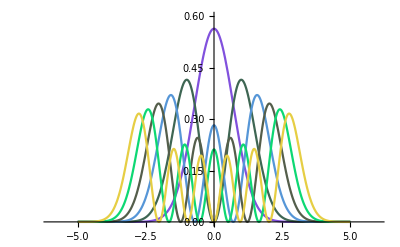

```mathematica
Show[gpn, PlotRange->{{-6,6},{0,0.6}}]
```

```mathematica
Subscript[Ν, N] =Sum[Sum[1,{n2,0,N-n1}], {n1, 0, N}]
```

1/2 (1+N) (2+N)

* **2-D N=4 with (n1=2, n2=2) & (n1=0,n2=4)***

```mathematica
Subscript[pψ, x2]=Subscript[pψ, x][[3]]/.{Subscript[x, 1]->x}
```

(ⅇ^(-x^2) (1-2 x^2)^2)/(2 √π)

```mathematica
Subscript[pψ, y2]=Subscript[pψ, x2]/.{x->y}//Simplify
```

(ⅇ^(-y^2) (1-2 y^2)^2)/(2 √π)

```mathematica
Subscript[pψ, x2,y2]=Subscript[pψ, y2]  Subscript[pψ, x2]//Simplify
```

(ⅇ^(-x^2-y^2) (1-2 x^2)^2 (1-2 y^2)^2)/(4 π)

```mathematica
Plot3D[Subscript[pψ, x2,y2],{x, -5,5},{y,-5,5},PlotRange->{0,0.2}]
```

-Graphics3D-

```mathematica
Subscript[pψ, x0]=Subscript[pψ, x][[1]]/.{Subscript[x, 1]->x}
```

(ⅇ^(-x^2))/(√π)

```mathematica
Subscript[pψ, x4]=Subscript[pψ, x][[5]]/.{Subscript[x, 1]->x}
```

(ⅇ^(-x^2) (3-12 x^2+4 x^4)^2)/(24 √π)

```mathematica
Subscript[pψ, y4]=Subscript[pψ, x4]/.{x->y}//Simplify
```

(ⅇ^(-y^2) (3-12 y^2+4 y^4)^2)/(24 √π)

```mathematica
Subscript[pψ, x0,y4]=Subscript[pψ, y4]  Subscript[pψ, x0]//Simplify
```

(ⅇ^(-x^2-y^2) (3-12 y^2+4 y^4)^2)/(24 π)

```mathematica
Plot3D[Subscript[pψ, x0,y4],{x, -5,5},{y,-5,5},PlotRange->{0,0.4}]
```

-Graphics3D-

Number of spherical harmonics.

```mathematica
Sum[4 k +1,{k,0,N/2}]
```

1/2 (1+N) (2+N)

```mathematica
Sum[2(2k-1)+1,{k,1,(N+1)/2}]//Factor
```

1/2 (1+N) (2+N)

```mathematica
Clear[z]
```

```mathematica
sperical =r  A  SphericalHarmonicY[1,-1,θ,ϕ]+ r B  SphericalHarmonicY[1,0,θ,ϕ]+ r C SphericalHarmonicY[1,1,θ,ϕ]
```

1/2 B √(3/π) r Cos[θ]+1/2 A ⅇ^(-ⅈ ϕ) √(3/(2 π)) r Sin[θ]-1/2 C ⅇ^(ⅈ ϕ) √(3/(2 π)) r Sin[θ]

```mathematica
sperical =ExpToTrig[sperical]//Simplify//Expand
```

1/2 B √(3/π) r Cos[θ]+1/2 A √(3/(2 π)) r Cos[ϕ] Sin[θ]-1/2 C √(3/(2 π)) r Cos[ϕ] Sin[θ]-1/2 ⅈ A √(3/(2 π)) r Sin[θ] Sin[ϕ]-1/2 ⅈ C √(3/(2 π)) r Sin[θ] Sin[ϕ]

```mathematica
%/.{r Sin[θ] Sin[ϕ] -> x, r Sin[θ] Cos[ϕ]->y, r Cos[θ]-> z}
```

-1/2 ⅈ A √(3/(2 π)) x-1/2 ⅈ C √(3/(2 π)) x+1/2 A √(3/(2 π)) y-1/2 C √(3/(2 π)) y+1/2 B √(3/π) z

```mathematica
opaa[j_,k_]@psi_:= SuperDagger[a][[j]]@a[[k]]@psi
```

```mathematica
Table[commutator[opaa[i,j],Η]@Ψ,{i,1,3},{j,1,3}]//Simplify//TableForm
```

0 | 0 | 0
0 | 0 | 0
0 | 0 | 0

normalization

```mathematica
Integrate[Subscript[ψ, 0x] Conjugate[Subscript[ψ, 0x]],{Subscript[x, 1],-Infinity,Infinity}]
```

(√π ℏ C[1]^2)/(√(M ω ℏ))

```mathematica
Solve[%==1, C[1]]//Flatten
```

{C[1]→-(M ω ℏ)^(1/4)/(π^(1/4) √ℏ),C[1]→(M ω ℏ)^(1/4)/(π^(1/4) √ℏ)}

```mathematica
Subscript[ψ, 0x]/.%[[2]]//Simplify
```

(ⅇ^(-(M ω x_1^2)/(2 ℏ)) ((M ω)/ℏ)^(1/4))/π^(1/4)

```mathematica
Subscript[ψ, nx][0]
```

ⅇ^(-(M ω x_1^2)/(2 ℏ)) C[1]

Transition P

```mathematica
pfψ = Table[Integrate[Subscript[ψ, nx][n] Conjugate[Subscript[ψ, nx][n]],{Subscript[x, 1],-Infinity,Infinity}],{n,5,6}]
```

{(120 √π ℏ C[1]^2)/(√(M ω ℏ)),720 √π √(ℏ/(M ω)) C[1]^2}

```mathematica
CC =1/Sqrt[pfψ/C[1]^2]//Simplify
```

{((M ω)/ℏ)^(1/4)/(2 √30 π^(1/4)),((M ω)/ℏ)^(1/4)/(12 √5 π^(1/4))}

```mathematica
Subscript[normlizedψ, 5x] =(CC[[1]] Subscript[ψ, nx][5]/C[1])//Simplify
```

(ⅈ ⅇ^(-(M ω x_1^2)/(2 ℏ)) (M ω)^(3/4) x_1 (15 ℏ^2-20 M ω ℏ x_1^2+4 M^2 ω^2 x_1^4))/(2 √15 π^(1/4) ℏ^(11/4))

```mathematica
Subscript[normlizedψ, 6x] =(CC[[2]] Subscript[ψ, nx][6]/C[1])//Simplify
```

(ⅇ^(-(M ω x_1^2)/(2 ℏ)) ((M ω)/ℏ)^(1/4) (15 ℏ^3-90 M ω ℏ^2 x_1^2+60 M^2 ω^2 ℏ x_1^4-8 M^3 ω^3 x_1^6))/(12 √5 π^(1/4) ℏ^3)

```mathematica
Subscript[x, 1,6,5]= Integrate[Conjugate[Subscript[normlizedψ, 6x]] Subscript[x, 1] Subscript[normlizedψ, 5x],{Subscript[x, 1], -Infinity,Infinity}]
```

-(ⅈ √3 ℏ)/(√(M ω ℏ))